## Simpleksna metoda

Sledeči program (spisal ga je doc. dr. Matjaž Konvalinka) po korakih izvaja simpleksno metodo.

```mathematica
Pivot[equations_,{xi_,xj_}]:=With[{sol=Solve[Select[equations,First[#]===xj&],xi][[1]]},Table[Expand[If[First[eqn]===xj,xi==(xi/.sol),eqn/.sol]],{eqn,equations}]//SortBy[#,First]&]

SimpleksnaMetoda[equations_,l___]:=With[{lst=List[l]},Print[TableForm[equations]];
If[Length[lst]>0,Print[];
SimpleksnaMetoda[Pivot[equations,First[lst]],Sequence@@Rest[lst]]]]
```

Funkcija Pivot je pomožna, funkcijo SimpleksnaMetoda pa uporabljate tako, da kot prvi argument vnesete slovar enačb, za tem pa naštevate pare vstopnih in izstopnih spremenljivk.

```mathematica
SimpleksnaMetoda[{
x4==5-2 x1-3 x2-x3,
x5==11-4 x1-3 x2-x3,
x6==8-3 x1-4 x2-2 x3,
z==5 x1+4 x2+3 x3
},{x2,x4},{x3,x6}]
```

x4==5-2 x1-3 x2-x3
x5==11-4 x1-3 x2-x3
x6==8-3 x1-4 x2-2 x3
z==5 x1+4 x2+3 x3

x2==5/3-(2 x1)/3-x3/3-x4/3
x5==6-2 x1+x4
x6==4/3-x1/3-(2 x3)/3+(4 x4)/3
z==20/3+(7 x1)/3+(5 x3)/3-(4 x4)/3

x2==1-x1/2-x4+x6/2
x3==2-x1/2+2 x4-(3 x6)/2
x5==6-2 x1+x4
z==10+(3 x1)/2+2 x4-(5 x6)/2

Preverite, ali so vaše rešitve pravilne. Prav tako lahko poizkušate, kaj se zgodi, če izberete napačno vstopno ali izstopno spremenljivko.

## Dvofazna metoda

Pri prvi fazi dvofazne metode ugotavljamo dopustnost problema z n spremenljivkami tako, da rešujemo problem z n+1 spremenljivkami. Če je n=2, si povezavo med problemoma lahko tudi predstavljamo.

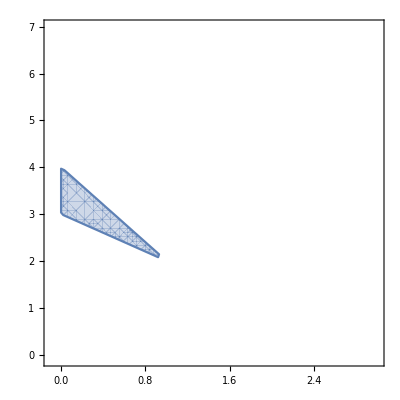

```mathematica
GraphicsRow[{
RegionPlot[x1-x2≤-1&&-x1-x2≤-3&&2x1+x2≤4&&x1≥0&&x2≥0,{x1,-0.1,3},{x2,-0.1,7}],
RegionPlot3D[x1-x2-x0≤-1&&-x1-x2-x0≤-3&&2x1+x2-x0≤4&&x1≥0&&x2≥0&&x0≥0,{x1,-0.1,3},{x2,-0.1,7},{x0,0,3},Mesh->False,PlotStyle->Directive[Opacity[0.5],PlotPoints->1000]]}]
```

Za katere vrednosti parametra a je sledeči problem dopusten? Pomagajte si z ukazom Manipulate.

x+y≥a
2x+y≥1
x+2y≤1
x,y≥0

min x+y

```mathematica
Manipulate[
Show[RegionPlot[x+y≥a&&2x+y≥1&&x+2y≤1,{x,0,1},{y,0,1}],
ContourPlot[{x+y==a,2x+y==1,x+2y==1},{x,0,1},{y,0,1}]],{a,0,1}]
```

## Končnost simpleksne metode

Pri izbiri vstopnih in izstopnih spremenljivk upoštevaj naslednji pravili:
i) Vstopna spremenljivka naj bo tista, ki ima največji koeficient v vrstici, ki ustreza funkcionalu z.
ii) Če imamo več kandidatov za izstopno spremenljivko, izberemo prvo po leksikografski ureditvi (x1 < x2 < x3 < x4 < x5 < x6 < x7).
Kaj opaziš?

```mathematica
SimpleksnaMetoda[{
x5==-1/2 x1+11/2 x2+5/2x3-9x4,
x6==-1/2 x1+3/2 x2+1/2x3-x4,
x7==1-x1,
z==10x1-57 x2-9 x3-24x4
},{x1,x5},{x2,x6},{x3,x1},{x4,x2},{x5,x3},{x6,x4}]
```

x5==-x1/2+(11 x2)/2+(5 x3)/2-9 x4
x6==-x1/2+(3 x2)/2+x3/2-x4
x7==1-x1
z==10 x1-57 x2-9 x3-24 x4

x1==11 x2+5 x3-18 x4-2 x5
x6==-4 x2-2 x3+8 x4+x5
x7==1-11 x2-5 x3+18 x4+2 x5
z==53 x2+41 x3-204 x4-20 x5

x1==-x3/2+4 x4+(3 x5)/4-(11 x6)/4
x2==-x3/2+2 x4+x5/4-x6/4
x7==1+x3/2-4 x4-(3 x5)/4+(11 x6)/4
z==(29 x3)/2-98 x4-(27 x5)/4-(53 x6)/4

x5==-x1/2+(11 x2)/2+(5 x3)/2-9 x4
x6==-x1/2+(3 x2)/2+x3/2-x4
x7==1-x1
z==10 x1-57 x2-9 x3-24 x4

x1==11 x2+5 x3-18 x4-2 x5
x6==-4 x2-2 x3+8 x4+x5
x7==1-11 x2-5 x3+18 x4+2 x5
z==53 x2+41 x3-204 x4-20 x5

x1==-x3/2+4 x4+(3 x5)/4-(11 x6)/4
x2==-x3/2+2 x4+x5/4-x6/4
x7==1+x3/2-4 x4-(3 x5)/4+(11 x6)/4
z==(29 x3)/2-98 x4-(27 x5)/4-(53 x6)/4

x2==x1-2 x4-x5/2+(5 x6)/2
x3==-2 x1+8 x4+(3 x5)/2-(11 x6)/2
x7==1-x1
z==-29 x1+18 x4+15 x5-93 x6

x3==2 x1-4 x2-x5/2+(9 x6)/2
x4==x1/2-x2/2-x5/4+(5 x6)/4
x7==1-x1
z==-20 x1-9 x2+(21 x5)/2-(141 x6)/2

x4==-x1/2+(3 x2)/2+x3/2-x6
x5==4 x1-8 x2-2 x3+9 x6
x7==1-x1
z==22 x1-93 x2-21 x3+24 x6

x5==-x1/2+(11 x2)/2+(5 x3)/2-9 x4
x6==-x1/2+(3 x2)/2+x3/2-x4
x7==1-x1
z==10 x1-57 x2-9 x3-24 x4

x1==11 x2+5 x3-18 x4-2 x5
x6==-4 x2-2 x3+8 x4+x5
x7==1-11 x2-5 x3+18 x4+2 x5
z==53 x2+41 x3-204 x4-20 x5

x1==-x3/2+4 x4+(3 x5)/4-(11 x6)/4
x2==-x3/2+2 x4+x5/4-x6/4
x7==1+x3/2-4 x4-(3 x5)/4+(11 x6)/4
z==(29 x3)/2-98 x4-(27 x5)/4-(53 x6)/4

x2==x1-2 x4-x5/2+(5 x6)/2
x3==-2 x1+8 x4+(3 x5)/2-(11 x6)/2
x7==1-x1
z==-29 x1+18 x4+15 x5-93 x6

x3==2 x1-4 x2-x5/2+(9 x6)/2
x4==x1/2-x2/2-x5/4+(5 x6)/4
x7==1-x1
z==-20 x1-9 x2+(21 x5)/2-(141 x6)/2

x4==-x1/2+(3 x2)/2+x3/2-x6
x5==4 x1-8 x2-2 x3+9 x6
x7==1-x1
z==22 x1-93 x2-21 x3+24 x6

x5==-x1/2+(11 x2)/2+(5 x3)/2-9 x4
x6==-x1/2+(3 x2)/2+x3/2-x4
x7==1-x1
z==10 x1-57 x2-9 x3-24 x4

x5==-x1/2+(11 x2)/2+(5 x3)/2-9 x4
x6==-x1/2+(3 x2)/2+x3/2-x4
x7==1-x1
z==10 x1-57 x2-9 x3-24 x4

x1==11 x2+5 x3-18 x4-2 x5
x6==-4 x2-2 x3+8 x4+x5
x7==1-11 x2-5 x3+18 x4+2 x5
z==53 x2+41 x3-204 x4-20 x5

x1==-x3/2+4 x4+(3 x5)/4-(11 x6)/4
x2==-x3/2+2 x4+x5/4-x6/4
x7==1+x3/2-4 x4-(3 x5)/4+(11 x6)/4
z==(29 x3)/2-98 x4-(27 x5)/4-(53 x6)/4

x2==x1-2 x4-x5/2+(5 x6)/2
x3==-2 x1+8 x4+(3 x5)/2-(11 x6)/2
x7==1-x1
z==-29 x1+18 x4+15 x5-93 x6

x3==2 x1-4 x2-x5/2+(9 x6)/2
x4==x1/2-x2/2-x5/4+(5 x6)/4
x7==1-x1
z==-20 x1-9 x2+(21 x5)/2-(141 x6)/2

x4==-x1/2+(3 x2)/2+x3/2-x6
x5==4 x1-8 x2-2 x3+9 x6
x7==1-x1
z==22 x1-93 x2-21 x3+24 x6

x5==-x1/2+(11 x2)/2+(5 x3)/2-9 x4
x6==-x1/2+(3 x2)/2+x3/2-x4
x7==1-x1
z==10 x1-57 x2-9 x3-24 x4

x2==x1-2 x4-x5/2+(5 x6)/2
x3==-2 x1+8 x4+(3 x5)/2-(11 x6)/2
x7==1-x1
z==-29 x1+18 x4+15 x5-93 x6

```mathematica
SimpleksnaMetoda[{
x5==-1/2 x1+11/2 x2+5/2x3-9x4,
x6==-1/2 x1+3/2 x2+1/2x3-x4,
x7==1-x1,
z==10x1-57 x2-9 x3-24x4
},{x1,x5},{x2,x6},{x3,x1},{x4,x2},{x5,x3},{x1,x4},{x3,x7}]
```

x5==-x1/2+(11 x2)/2+(5 x3)/2-9 x4
x6==-x1/2+(3 x2)/2+x3/2-x4
x7==1-x1
z==10 x1-57 x2-9 x3-24 x4

x1==11 x2+5 x3-18 x4-2 x5
x6==-4 x2-2 x3+8 x4+x5
x7==1-11 x2-5 x3+18 x4+2 x5
z==53 x2+41 x3-204 x4-20 x5

x1==-x3/2+4 x4+(3 x5)/4-(11 x6)/4
x2==-x3/2+2 x4+x5/4-x6/4
x7==1+x3/2-4 x4-(3 x5)/4+(11 x6)/4
z==(29 x3)/2-98 x4-(27 x5)/4-(53 x6)/4

x2==x1-2 x4-x5/2+(5 x6)/2
x3==-2 x1+8 x4+(3 x5)/2-(11 x6)/2
x7==1-x1
z==-29 x1+18 x4+15 x5-93 x6

x3==2 x1-4 x2-x5/2+(9 x6)/2
x4==x1/2-x2/2-x5/4+(5 x6)/4
x7==1-x1
z==-20 x1-9 x2+(21 x5)/2-(141 x6)/2

x4==-x1/2+(3 x2)/2+x3/2-x6
x5==4 x1-8 x2-2 x3+9 x6
x7==1-x1
z==22 x1-93 x2-21 x3+24 x6

x1==3 x2+x3-2 x4-2 x6
x5==4 x2+2 x3-8 x4+x6
x7==1-3 x2-x3+2 x4+2 x6
z==-27 x2+x3-44 x4-20 x6

x1==1-x7
x3==1-3 x2+2 x4+2 x6-x7
x5==2-2 x2-4 x4+5 x6-2 x7
z==1-30 x2-42 x4-18 x6-x7

Zgornji linearni program reši še s pomočjo Blandovega pravila (tako vstopne kot izstopne spremenljivke izbiraš glede na leksikografsko ureditev).

## Celoštevilsko linearno programiranje

Poiščite optimalno rešitev sledečega problema:

2x1+x2≤6
2x1+3x2≤9
x1,x2≥0

max 3x1+4x2

Nato poiščite še optimalno rešitev v primeru, da sta x1 in x2 celoštevilski spremenljivki.

Nazadnje poiščite isto optimalno rešitev še na roke, torej tako, da ne izkoristite tega, da zna Mathematica reševati tudi celoštevilske probleme.

```mathematica
Manipulate[
Show[RegionPlot[2x1+x2≤6&&2x1+3x2≤9,{x1,0,4},{x2,0,4}],ContourPlot[{2x1+x2==6,2x1+3x2==9,3x1+4x2==k},{x1,0,4},{x2,0,4}],
Graphics[Table[Point[{x1,x2}],{x1,0,4},{x2,0,4}]]],{k,0,20}]
```

```mathematica
Maximize[{3x1+4x2,2x1+x2≤ 6,2x1+3x2≤9,x1≥0,x2≥0},{x1,x2},Integers]
```

{12,{x1→0,x2→3}}

## 0-1 nahrbtnik

Rešite problem 0-1 nahrbtnika z volumnom 10 in naslednjimi predmeti:

volumen | cena
2 | 30
4 | 60
6 | 50
3 | 40

```mathematica
Maximize[{30x1+60x2+50x3+40x4,2x1+4x2+6x3+3x4≤10,0≤x1≤1,0≤x2≤1,0≤x3≤1,0≤x4≤1},{x1,x2,x3,x4},Integers]
```

{130,{x1→1,x2→1,x3→0,x4→1}}